## Bleach Correction for Z-stack images

```mathematica
(* There must be a maximum intensity projection along z, named MAX_filename.tif
   and a maximum intensity projection along z and time, named MAX_MAX_filename.tif in the same directory*)
```

### Choosing a file, and reading in

```mathematica
{FileNameSetter[Dynamic@myFile],Dynamic@myFile}
```

```mathematica
{$CellContext`myFileOpenAll,}
```

{$CellContext`myFileOpenAll,}

```mathematica
(*numColor=3;*)
numColor=3; (*write the number of channels recorded on your movie*)
numZstack=13; (*write the number of Z stacks collected on your movie*)
myZmovie=Thread/@Transpose@Partition[Partition[Import@myFile,numColor],numZstack];
```

### Making Masks

```mathematica
(*maxmaxImg=Import@(DirectoryName@#<>"MAX_MAX_"<>FileNameTake@#&@myFile);*)
maxmaxImg=Import@(DirectoryName@#<>"MAX_"<>FileNameTake@#&@myFile);
```

#### channel 1

```mathematica
Manipulate[ImageAdjust[maxmaxImg⟦1⟧,{0,0,1},{threshold1,threshold2}],
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1,threshold2}],
{threshold1,0,0.2,0.001},{{threshold2,0.1},0,1,0.001}]
```

```mathematica
ImageAdjust[maxmaxImg⟦1⟧,{0,0,1},thtemp]
```

```mathematica
myMaskCh1=-Graphics-;(*paste the image generated above here*)
```

#### channel 2

```mathematica
Manipulate[ImageAdjust[maxmaxImg⟦2⟧,{0,0,1},{threshold1,threshold2}],
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1,threshold2}],
{threshold1,0,0.2,0.001},{{threshold2,0.1},0,1,0.001}]
```

```mathematica
ImageAdjust[maxmaxImg⟦2⟧,{0,0,1},thtemp]
```

```mathematica
myMaskCh2=-Graphics-;(*paste the image generated above here*)
```

#### channel 3

```mathematica
Manipulate[ImageAdjust[maxmaxImg⟦3⟧,{0,0,1},{threshold1,threshold2}],
Button["Choose threshold such that the shape of the cell can be visualized and CLICK",thtemp={threshold1,threshold2}],
{threshold1,0,0.2,0.001},{{threshold2,0.1},0,1,0.001}]
```

```mathematica
ImageAdjust[maxmaxImg⟦3⟧,{0,0,1},thtemp]
```

```mathematica
myMaskCh3=-Graphics-;(*paste the image generated above here*)
```

### Correcting movies for photo bleaching and laser fluctuation in each z-stack

```mathematica
meanIntCh1=(ComponentMeasurements[ImageMultiply[myMaskCh1,#],"Mean"]&/@#⟦1⟧&/@myZmovie)⟦All,All,1,2⟧;
meanIntCh1/=Mean@Mean@meanIntCh1⟦All,;;5⟧;
meanIntCh2=(ComponentMeasurements[ImageMultiply[myMaskCh2,#],"Mean"]&/@#⟦2⟧&/@myZmovie)⟦All,All,1,2⟧;
meanIntCh2/=Mean@Mean@meanIntCh2⟦All,;;5⟧;
meanIntCh3=(ComponentMeasurements[ImageMultiply[myMaskCh3,#],"Mean"]&/@#⟦3⟧&/@myZmovie)⟦All,All,1,2⟧;
meanIntCh3/=Mean@Mean@meanIntCh3⟦All,;;5⟧;
```

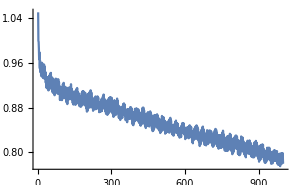
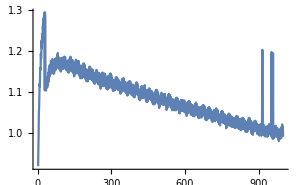
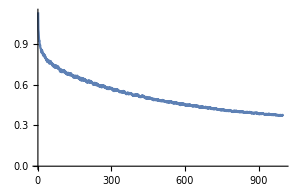

```mathematica
ListLinePlot[#,PlotRange->All,ImageSize->300]&/@{meanIntCh1,meanIntCh2,meanIntCh3}
```

```mathematica
blcCh1=myZmovie⟦All,1⟧/meanIntCh1;
blcCh2=myZmovie⟦All,2⟧/meanIntCh2;
blcCh3=myZmovie⟦All,3⟧/meanIntCh3;
```

### Exporting File

```mathematica
myBLCZmovie=Flatten@Transpose@(Thread/@Thread@{blcCh1,blcCh2,blcCh3});
```

```mathematica
Export[DirectoryName@#<>"BLC_"<>FileNameTake@#&@myFile,myBLCZmovie];
If[ValueQ@blcMaxImg,Export[DirectoryName@#<>"BLC_MAX_"<>FileNameTake@#&@myFile,blcMaxImg]];
```